```mathematica
data=ToExpression[StringSplit[Import["E:\\1 - research\\4.7 - 3D ising\\non-trivial-VUMPS\\0.1 10.txt"]]]
```

{8,12,16,20,24,28,32,48,64,-4.05307,-4.05257,-4.05256,-4.05256,-4.05256,-4.05255,-4.05256,-4.05256,-4.05256,-5+3.73532 e,-5+1.36507 e,-5+2.61253 e,-5+1.51191 e,-5+1.02889 e,-5+1.29533 e,-5+1.19281 e,-6+5.50514 e,-6+6.84607 e}

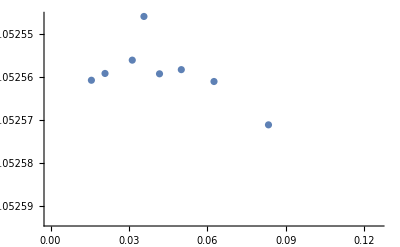

```mathematica
x=data[[1;;9]];
y=data[[10;;18]];
ListPlot[Transpose[{1/x,y}]]
```

```mathematica
Fit[Transpose[{1/x,y}], {1,t},t]
```

-4.05241-0.0040215 t

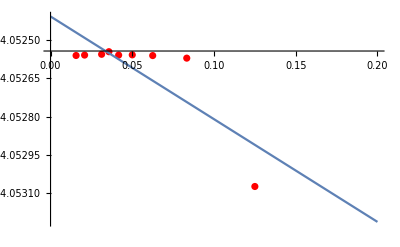

```mathematica
Show[ListPlot[Transpose[{1/x,y}],PlotStyle->Red],Plot[-4.052407937808855-0.004021498413822201 t,{t,0,0.2}],PlotRange->All]
```

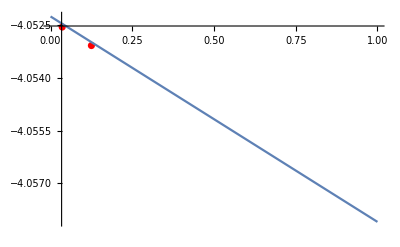

```mathematica
Show[ListPlot[Transpose[{1/x,y}],PlotStyle->Red],Plot[-4.052244715582676-0.005851550785236552 t,{t,0,1}]]
```